# Nanobot Theory : Data Analysis and Plotting

#### Yibin Jiang, Abhishek Sharma Cronin Lab University of Glasgow

```mathematica
baseDirectory=NotebookDirectory[];
data=Reverse[Import[baseDirectory<>"/data/C_cross_0.csv"],2];
d=0.41/1000;
```

```mathematica
dipoleLength=Quantity[0.41,"nm"];
```

```mathematica
d=QuantityMagnitude[10^-3 dipoleLength]; (* For plotting 10^-3 is a scaling factor *)
```

```mathematica
finalstructure = Import[baseDirectory<>"/data/final_structure_0.csv"];
```

```mathematica
wavelength = Table[0.39+0.01*i,{i,51}];
```

```mathematica
plotUVVis[index_]:= Block[{Au,structure,reffi,tempData,intp,plot1,plot2,fig},
Au=finalstructure⟦1;;1329+index⟧;
structure=Graphics3D[{Yellow,Opacity[0.5],Sphere[Au,1/2]},Boxed->False,ViewProjection->"Orthographic",ViewPoint->{2,-2,1},ImageSize->{300,300}];
reffi=(3/(4π)d^3 Length@Au )^(1/3);
tempData=Transpose[{1000*wavelength,data⟦All,1+index⟧/(π reffi^2)}];
intp=Interpolation[tempData,InterpolationOrder->2];
plot1=Plot[intp[x],{x,400,900},PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotRange->{0,12}];
plot2=ListPlot[tempData,PlotStyle->{Black,PointSize[0.02]},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]}];
fig=Show[{plot1,plot2},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame-> True,FrameLabel->{"Wavelength (nm)","Extinction"},AspectRatio->1,ImageSize->300,PlotRange->{0,8.2}];{structure,fig}]
```

```mathematica
restylePlot2[p_,op:OptionsPattern[ListLinePlot]]:=ListLinePlot[Cases[Normal@p,Line[x__]:>x,∞],op,Options[p]];
```

```mathematica
intermediates=Flatten@{0,408,420,416,396,360,308,240,156,56};
intermediateposition =Table[Total[intermediates⟦1;;i⟧],{i,Length[intermediates]}];
```

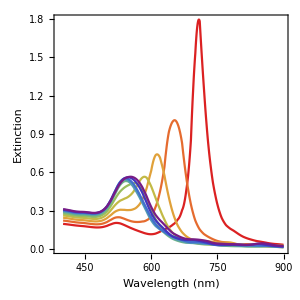

Z:\group\Yibin Jiang\Papers\Nanobot_Theory\Code\Small_rod_to_octahedra\/Combined_UV.png

```mathematica
plots = Flatten@{Table[plotUVVis[i]⟦2⟧,{i,intermediateposition}]};
f = restylePlot2[plots,PlotStyle->Reverse@Table[ColorData["Rainbow"][i],{i,0,1,1/(Length[plots]-1)}],FrameStyle->Directive[16,FontColor->Black],PlotRange->All,AspectRatio->1,ImageSize->300,Frame-> True,FrameLabel->{"Wavelength (nm)","Extinction"}]
Export[NotebookDirectory[]<>"/Combined_UV.png",f,ImageResolution->300]
```